# Fitting Motor Velocity Data

Cole Welch
26 August 2018

We explore extracting time constants from motor model expressions.

## Section. Introduction

### Section.Subsection. Administrivia

Before we begin, we load in some previously computed logic (Ref: https://github.com/rgatkinson/RobotPhysics/blob/master/MotorPhysics-GearsInitialConditions.pdf)

```mathematica
Get[NotebookDirectory[] <> "Utilities.m"]
inputDirectory = FileNameJoin[{NotebookDirectory[],"MotorPhysicsGearsInitialConditions.Output"}] <> $PathnameSeparator;
Get[inputDirectory <> "ParametersUnitsAndAssumptions.m"];
Get[inputDirectory <> "MotorModels.m"];
Get[inputDirectory <> "MotorTimeDomainFunctions.m"];
Get[inputDirectory <> "Misc.m"];
```

```mathematica
SetOptions[Plot,LabelStyle->Directive[Background->None]];
prettyPrintFontSize = 20;
framed[expr_] := Framed[expr, FrameStyle->Darker[Green]]
```

## 2. Motor Velocity Expression

Let’s refresh ourselves as to the parameter values of sample AndyMark 40s.

```mathematica
motorParameters["AM 40 A"]//N
```

<|R→2.5 W/A^2,L→0.000674 H,Ν→40.,η→0.9,Ke→0.018825 kg m^2/(s^2 A rad),Kt→0.018825 kg m^2/(s^2 A rad),B→0.000157569 kg m^2/(s rad^2),J→1.54236×10^-8 kg m^2/rad^2,Jafter→0. kg m^2/rad^2,Bafter→0. kg m^2/(s rad^2),ΔτappConst→0. kg m^2/(s^2 rad)|>

```mathematica
motorParameters["AM 40 B"]//N
```

<|R→3.8 W/A^2,L→0.000705 H,Ν→40.,η→0.9,Ke→0.017625 kg m^2/(s^2 A rad),Kt→0.017625 kg m^2/(s^2 A rad),B→0.000388889 kg m^2/(s rad^2),J→1.20903×10^-8 kg m^2/rad^2,Jafter→0. kg m^2/rad^2,Bafter→0. kg m^2/(s rad^2),ΔτappConst→0. kg m^2/(s^2 rad)|>

```mathematica
motorParameters["AM 40 C"]//N
```

<|R→2.1 W/A^2,L→0.000716 H,Ν→40.,η→0.9,Ke→0.019075 kg m^2/(s^2 A rad),Kt→0.019075 kg m^2/(s^2 A rad),B→0.0000125 kg m^2/(s rad^2),J→1.71597×10^-8 kg m^2/rad^2,Jafter→0. kg m^2/rad^2,Bafter→0. kg m^2/(s rad^2),ΔτappConst→0. kg m^2/(s^2 rad)|>

We show a list of the variables present in our expression for the velocity time domain expression for a motor.

```mathematica
velAfterStepGeneric // variables
```

{B,Bafter,J,Jafter,Ke,Kt,L,R,t,vapp0,ΔvappConst,ΔτappConst,η,Ν,τapp0}

We substitute what we know about our situation. However, we do not simply plug in “AM 40 A/B/C,” since some of our parameters are going to be different from those of a general motor. We also average each of the parameter values we do use over all the motors that have already been tested.

```mathematica
velSubExpr=velAfterStepGeneric/.{B->0.000186,J->1.49*10^-8,Ke->0.0184,Kt->0.0184,L->0.000697,R->1.2,vapp0->0,ΔvappConst->13,ΔτappConst->0,τapp0->0,Ν->40}//FullSimplify//N
```

-((0.0133378 (Jafter+0.00002384 η) η ((-1.+2.71828^((t (-0.5 Bafter-860.832 Jafter-0.169322 η+717.36 √(4.85809×10^-7 Bafter^2-0.0016728 Bafter Jafter+1.44 Jafter^2+2.49274×10^-7 Bafter η-0.00193941 Jafter η-4.02802×10^-9 η^2)))/(Jafter+0.00002384 η)))/(0.000697 Bafter+1.2 Jafter+0.000236035 η-1. √(4.85809×10^-7 Bafter^2-0.0016728 Bafter Jafter+1.44 Jafter^2+2.49274×10^-7 Bafter η-0.00193941 Jafter η-4.02802×10^-9 η^2))-(1. (-1.+2.71828^(-(717.36 t (0.000697 Bafter+1.2 Jafter+0.000236035 η+√(4.85809×10^-7 Bafter^2-0.0016728 Bafter Jafter+1.44 Jafter^2+2.49274×10^-7 Bafter η-0.00193941 Jafter η-4.02802×10^-9 η^2)))/(Jafter+0.00002384 η))))/(0.000697 Bafter+1.2 Jafter+0.000236035 η+√(4.85809×10^-7 Bafter^2-0.0016728 Bafter Jafter+1.44 Jafter^2+2.49274×10^-7 Bafter η-0.00193941 Jafter η-4.02802×10^-9 η^2))))/(√(4.85809×10^-7 Bafter^2-0.0016728 Bafter Jafter+1.44 Jafter^2+2.49274×10^-7 Bafter η-0.00193941 Jafter η-4.02802×10^-9 η^2)))

## 3. Data Fitting

#### 3.1. Data Set 1

We are now ready to import the motor velocity step response data that we are going to fit. Note: we have to remove the extra set of brackets on the table to use the data.

```mathematica
data1=Import["C:\RobotPhysics\3 Wheel Robot Encoder Rotational Velocity Test Data.xlsx",{"Data",1}]
```

{{0.,0.},{0.008,0.},{0.016,0.},{0.024,15.625},{0.032,155.},{0.04,305.},{0.048,520.},{0.056,785.},{0.064,1040.},{0.072,1270.},{0.08,1455.},{0.088,1570.},{0.096,1615.},{0.104,1620.},{0.112,1585.},{0.12,1530.},{0.128,1475.},{0.136,1420.},{0.144,1365.},{0.152,1335.},{0.16,1315.},{0.168,1295.},{0.176,1290.},{0.184,1300.},{0.192,1320.},{0.2,1350.},{0.208,1410.},{0.216,1465.},{0.224,1530.},{0.232,1590.},{0.24,1650.},{0.248,1685.},{0.256,1745.},{0.264,1795.},{0.272,1840.},{0.28,1880.},{0.288,1925.},{0.296,1945.},{0.304,1970.},{0.312,1990.},{0.32,2015.},{0.328,2025.},{0.336,2045.},{0.344,2050.},{0.352,2065.},{0.36,2065.},{0.368,2090.},{0.376,2105.},{0.384,2125.},{0.392,2130.},{0.4,2145.},{0.408,2140.},{0.416,2135.},{0.424,2130.},{0.432,2130.},{0.44,2125.},{0.448,2130.},{0.456,2135.},{0.464,2150.},{0.472,2170.},{0.48,2190.},{0.488,2205.},{0.496,2220.},{0.504,2225.},{0.512,2225.},{0.52,2225.},{0.528,2230.},{0.536,2240.},{0.544,2245.},{0.552,2265.},{0.56,2270.},{0.568,2270.},{0.576,2265.},{0.584,2265.},{0.592,2240.},{0.6,2245.},{0.608,2250.},{0.616,2255.},{0.624,2270.},{0.632,2305.},{0.64,2330.},{0.648,2360.},{0.656,2385.},{0.664,2400.},{0.672,2395.},{0.68,2385.},{0.688,2375.},{0.696,2375.},{0.704,2370.},{0.712,2375.},{0.72,2385.},{0.728,2390.},{0.736,2390.},{0.744,2400.},{0.752,2415.},{0.76,2420.},{0.768,2420.},{0.776,2425.},{0.784,2420.},{0.792,2415.},{0.8,2415.},{0.808,2415.},{0.816,2410.},{0.824,2415.},{0.832,2410.},{0.84,2410.},{0.848,2420.},{0.856,2435.},{0.864,2445.},{0.872,2455.},{0.88,2460.},{0.888,2460.},{0.896,2450.},{0.904,2445.},{0.912,2450.},{0.92,2465.},{0.928,2485.},{0.936,2525.},{0.944,2555.},{0.952,2575.},{0.96,2590.},{0.968,2585.},{0.976,2550.},{0.984,2525.},{0.992,2505.},{1.,2465.},{1.008,2455.},{1.016,2455.},{1.024,2455.},{1.032,2460.},{1.04,2480.},{1.048,2485.},{1.056,2500.},{1.064,2510.},{1.072,2510.},{1.08,2510.},{1.088,2510.},{1.096,2505.},{1.104,2495.},{1.112,2495.},{1.12,2490.},{1.128,2485.},{1.136,2480.},{1.144,2475.},{1.152,2470.},{1.16,2475.},{1.168,2485.},{1.176,2495.},{1.184,2515.},{1.192,2545.},{1.2,2560.},{1.208,2570.},{1.216,2585.},{1.224,2590.},{1.232,2555.},{1.24,2540.},{1.248,2525.},{1.256,2500.},{1.264,2485.},{1.272,2505.},{1.28,2510.},{1.288,2510.},{1.296,2520.},{1.304,2525.},{1.312,2515.},{1.32,2520.},{1.328,2530.},{1.336,2530.},{1.344,2530.},{1.352,2540.},{1.36,2530.},{1.368,2525.},{1.376,2525.},{1.384,2530.},{1.392,2525.},{1.4,2535.},{1.408,2540.},{1.416,2545.},{1.424,2540.},{1.432,2540.},{1.44,2535.},{1.448,2530.},{1.456,2520.},{1.464,2515.},{1.472,2510.},{1.48,2505.},{1.488,2490.},{1.496,2490.},{1.504,2490.},{1.512,2490.},{1.52,2490.},{1.528,2510.},{1.536,2515.},{1.544,2520.},{1.552,2525.},{1.56,2530.},{1.568,2515.},{1.576,2510.},{1.584,2510.},{1.592,2515.},{1.6,2515.},{1.608,2535.},{1.616,2545.},{1.624,2550.},{1.632,2545.},{1.64,2555.},{1.648,2565.},{1.656,2570.},{1.664,2570.},{1.672,2575.},{1.68,2565.},{1.688,2535.},{1.696,2525.},{1.704,2520.},{1.712,2520.},{1.72,2525.},{1.728,2540.},{1.736,2545.},{1.744,2550.},{1.752,2550.},{1.76,2555.},{1.768,2555.},{1.776,2560.},{1.784,2560.},{1.792,2560.},{1.8,2550.},{1.808,2555.},{1.816,2545.},{1.824,2545.},{1.832,2545.},{1.84,2550.},{1.848,2540.},{1.856,2550.},{1.864,2560.},{1.872,2565.},{1.88,2570.},{1.888,2580.},{1.896,2575.},{1.904,2555.},{1.912,2550.},{1.92,2540.},{1.928,2530.},{1.936,2525.},{1.944,2540.},{1.952,2530.},{1.96,2530.}}

Change the velocity units from ticks / second to radians / second.

```mathematica
data1={#[[1]],2Pi/1120*#[[2]]}&/@data1
```

{{0.,0.},{0.008,0.},{0.016,0.},{0.024,0.087656},{0.032,0.869548},{0.04,1.71105},{0.048,2.91719},{0.056,4.40384},{0.064,5.83439},{0.072,7.12468},{0.08,8.16253},{0.088,8.80768},{0.096,9.06013},{0.104,9.08818},{0.112,8.89183},{0.12,8.58328},{0.128,8.27473},{0.136,7.96618},{0.144,7.65763},{0.152,7.48933},{0.16,7.37713},{0.168,7.26493},{0.176,7.23688},{0.184,7.29298},{0.192,7.40518},{0.2,7.57348},{0.208,7.91008},{0.216,8.21863},{0.224,8.58328},{0.232,8.91988},{0.24,9.25648},{0.248,9.45283},{0.256,9.78943},{0.264,10.0699},{0.272,10.3224},{0.28,10.5468},{0.288,10.7992},{0.296,10.9114},{0.304,11.0517},{0.312,11.1639},{0.32,11.3041},{0.328,11.3602},{0.336,11.4724},{0.344,11.5005},{0.352,11.5846},{0.36,11.5846},{0.368,11.7249},{0.376,11.809},{0.384,11.9212},{0.392,11.9493},{0.4,12.0334},{0.408,12.0054},{0.416,11.9773},{0.424,11.9493},{0.432,11.9493},{0.44,11.9212},{0.448,11.9493},{0.456,11.9773},{0.464,12.0615},{0.472,12.1737},{0.48,12.2859},{0.488,12.37},{0.496,12.4542},{0.504,12.4822},{0.512,12.4822},{0.52,12.4822},{0.528,12.5103},{0.536,12.5664},{0.544,12.5944},{0.552,12.7066},{0.56,12.7347},{0.568,12.7347},{0.576,12.7066},{0.584,12.7066},{0.592,12.5664},{0.6,12.5944},{0.608,12.6225},{0.616,12.6505},{0.624,12.7347},{0.632,12.931},{0.64,13.0713},{0.648,13.2396},{0.656,13.3798},{0.664,13.464},{0.672,13.4359},{0.68,13.3798},{0.688,13.3237},{0.696,13.3237},{0.704,13.2957},{0.712,13.3237},{0.72,13.3798},{0.728,13.4079},{0.736,13.4079},{0.744,13.464},{0.752,13.5481},{0.76,13.5762},{0.768,13.5762},{0.776,13.6042},{0.784,13.5762},{0.792,13.5481},{0.8,13.5481},{0.808,13.5481},{0.816,13.5201},{0.824,13.5481},{0.832,13.5201},{0.84,13.5201},{0.848,13.5762},{0.856,13.6603},{0.864,13.7164},{0.872,13.7725},{0.88,13.8006},{0.888,13.8006},{0.896,13.7445},{0.904,13.7164},{0.912,13.7445},{0.92,13.8286},{0.928,13.9408},{0.936,14.1652},{0.944,14.3335},{0.952,14.4457},{0.96,14.5299},{0.968,14.5018},{0.976,14.3055},{0.984,14.1652},{0.992,14.053},{1.,13.8286},{1.008,13.7725},{1.016,13.7725},{1.024,13.7725},{1.032,13.8006},{1.04,13.9128},{1.048,13.9408},{1.056,14.025},{1.064,14.0811},{1.072,14.0811},{1.08,14.0811},{1.088,14.0811},{1.096,14.053},{1.104,13.9969},{1.112,13.9969},{1.12,13.9689},{1.128,13.9408},{1.136,13.9128},{1.144,13.8847},{1.152,13.8567},{1.16,13.8847},{1.168,13.9408},{1.176,13.9969},{1.184,14.1091},{1.192,14.2774},{1.2,14.3616},{1.208,14.4177},{1.216,14.5018},{1.224,14.5299},{1.232,14.3335},{1.24,14.2494},{1.248,14.1652},{1.256,14.025},{1.264,13.9408},{1.272,14.053},{1.28,14.0811},{1.288,14.0811},{1.296,14.1372},{1.304,14.1652},{1.312,14.1091},{1.32,14.1372},{1.328,14.1933},{1.336,14.1933},{1.344,14.1933},{1.352,14.2494},{1.36,14.1933},{1.368,14.1652},{1.376,14.1652},{1.384,14.1933},{1.392,14.1652},{1.4,14.2213},{1.408,14.2494},{1.416,14.2774},{1.424,14.2494},{1.432,14.2494},{1.44,14.2213},{1.448,14.1933},{1.456,14.1372},{1.464,14.1091},{1.472,14.0811},{1.48,14.053},{1.488,13.9689},{1.496,13.9689},{1.504,13.9689},{1.512,13.9689},{1.52,13.9689},{1.528,14.0811},{1.536,14.1091},{1.544,14.1372},{1.552,14.1652},{1.56,14.1933},{1.568,14.1091},{1.576,14.0811},{1.584,14.0811},{1.592,14.1091},{1.6,14.1091},{1.608,14.2213},{1.616,14.2774},{1.624,14.3055},{1.632,14.2774},{1.64,14.3335},{1.648,14.3896},{1.656,14.4177},{1.664,14.4177},{1.672,14.4457},{1.68,14.3896},{1.688,14.2213},{1.696,14.1652},{1.704,14.1372},{1.712,14.1372},{1.72,14.1652},{1.728,14.2494},{1.736,14.2774},{1.744,14.3055},{1.752,14.3055},{1.76,14.3335},{1.768,14.3335},{1.776,14.3616},{1.784,14.3616},{1.792,14.3616},{1.8,14.3055},{1.808,14.3335},{1.816,14.2774},{1.824,14.2774},{1.832,14.2774},{1.84,14.3055},{1.848,14.2494},{1.856,14.3055},{1.864,14.3616},{1.872,14.3896},{1.88,14.4177},{1.888,14.4738},{1.896,14.4457},{1.904,14.3335},{1.912,14.3055},{1.92,14.2494},{1.928,14.1933},{1.936,14.1652},{1.944,14.2494},{1.952,14.1933},{1.96,14.1933}}

Here is a plot of the data.

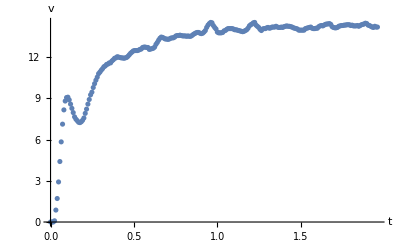

```mathematica
ListPlot[data1,AxesLabel->{t,v}]
```

```mathematica
Length[data1]
```

246

We’re ready to fit.

```mathematica
nlm1=NonlinearModelFit[data1,velSubExpr,{Bafter,Jafter,η},t]
```

FittedModel[-0.638208 (-0.0644725 (-1.+2.71828^(-1717.67 t))+22.0794 (-1.+2.71828^(-5.01565 t)))]

Here is a comparison between the data and our fit.  They appear to follow each other quite closely.

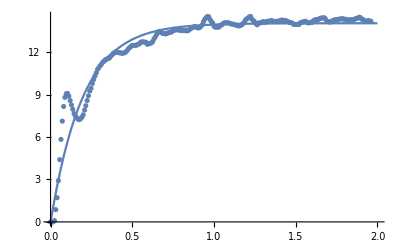

```mathematica
Show[Plot[nlm1[t],{t,0,2},PlotRange->All],ListPlot[data1], AxesOrigin->{0,0}]
```

Here are our fit parameters.  However, they are clearly incorrect.  Additionally, they appear to be very unstable if any of the initial conditions are changed at all, so we may be overfitting our data.

```mathematica
nlm1["BestFitParameters"]
```

{Bafter→-10.3683,Jafter→6.47636,η→57.1191}

#### 3.1. Data Set 2

We repeat the steps from Data Set 1 for our remaining data sets.

```mathematica
data2=Import["C:\RobotPhysics\3 Wheel Robot Encoder Rotational Velocity Test Data.xlsx",{"Data",2}]
```

{{0.,0.},{0.008,0.},{0.016,0.},{0.024,7.8125},{0.032,140.},{0.04,290.},{0.048,500.},{0.056,770.},{0.064,1030.},{0.072,1270.},{0.08,1450.},{0.088,1565.},{0.096,1595.},{0.104,1570.},{0.112,1495.},{0.12,1400.},{0.128,1300.},{0.136,1220.},{0.144,1165.},{0.152,1140.},{0.16,1145.},{0.168,1165.},{0.176,1190.},{0.184,1235.},{0.192,1285.},{0.2,1345.},{0.208,1415.},{0.216,1495.},{0.224,1565.},{0.232,1635.},{0.24,1685.},{0.248,1730.},{0.256,1760.},{0.264,1785.},{0.272,1810.},{0.28,1845.},{0.288,1870.},{0.296,1905.},{0.304,1935.},{0.312,1960.},{0.32,1975.},{0.328,1995.},{0.336,2010.},{0.344,2025.},{0.352,2035.},{0.36,2050.},{0.368,2060.},{0.376,2065.},{0.384,2075.},{0.392,2075.},{0.4,2070.},{0.408,2070.},{0.416,2065.},{0.424,2055.},{0.432,2060.},{0.44,2070.},{0.448,2075.},{0.456,2090.},{0.464,2110.},{0.472,2130.},{0.48,2150.},{0.488,2175.},{0.496,2195.},{0.504,2210.},{0.512,2225.},{0.52,2230.},{0.528,2230.},{0.536,2235.},{0.544,2240.},{0.552,2240.},{0.56,2245.},{0.568,2250.},{0.576,2250.},{0.584,2250.},{0.592,2255.},{0.6,2265.},{0.608,2280.},{0.616,2295.},{0.624,2315.},{0.632,2330.},{0.64,2340.},{0.648,2340.},{0.656,2345.},{0.664,2345.},{0.672,2345.},{0.68,2340.},{0.688,2345.},{0.696,2345.},{0.704,2345.},{0.712,2345.},{0.72,2360.},{0.728,2370.},{0.736,2380.},{0.744,2395.},{0.752,2415.},{0.76,2415.},{0.768,2420.},{0.776,2425.},{0.784,2415.},{0.792,2400.},{0.8,2400.},{0.808,2390.},{0.816,2385.},{0.824,2395.},{0.832,2400.},{0.84,2405.},{0.848,2415.},{0.856,2420.},{0.864,2425.},{0.872,2435.},{0.88,2440.},{0.888,2445.},{0.896,2445.},{0.904,2435.},{0.912,2430.},{0.92,2415.},{0.928,2405.},{0.936,2405.},{0.944,2410.},{0.952,2415.},{0.96,2435.},{0.968,2450.},{0.976,2465.},{0.984,2485.},{0.992,2490.},{1.,2495.},{1.008,2500.},{1.016,2495.},{1.024,2480.},{1.032,2480.},{1.04,2475.},{1.048,2465.},{1.056,2460.},{1.064,2470.},{1.072,2480.},{1.08,2485.},{1.088,2500.},{1.096,2515.},{1.104,2520.},{1.112,2515.},{1.12,2520.},{1.128,2520.},{1.136,2515.},{1.144,2505.},{1.152,2500.},{1.16,2490.},{1.168,2480.},{1.176,2480.},{1.184,2485.},{1.192,2490.},{1.2,2495.},{1.208,2505.},{1.216,2510.},{1.224,2510.},{1.232,2510.},{1.24,2510.},{1.248,2500.},{1.256,2490.},{1.264,2500.},{1.272,2500.},{1.28,2500.},{1.288,2505.},{1.296,2510.},{1.304,2490.},{1.312,2490.},{1.32,2495.},{1.328,2500.},{1.336,2505.},{1.344,2520.},{1.352,2525.},{1.36,2515.},{1.368,2510.},{1.376,2505.},{1.384,2500.},{1.392,2495.},{1.4,2505.},{1.408,2510.},{1.416,2515.},{1.424,2520.},{1.432,2530.},{1.44,2535.},{1.448,2535.},{1.456,2540.},{1.464,2545.},{1.472,2535.},{1.48,2530.},{1.488,2530.},{1.496,2520.},{1.504,2510.},{1.512,2515.},{1.52,2510.},{1.528,2510.},{1.536,2530.},{1.544,2550.},{1.552,2565.},{1.56,2590.},{1.568,2605.},{1.576,2590.},{1.584,2575.},{1.592,2555.},{1.6,2525.},{1.608,2500.},{1.616,2495.},{1.624,2485.},{1.632,2490.},{1.64,2500.},{1.648,2510.},{1.656,2515.},{1.664,2530.},{1.672,2530.},{1.68,2530.},{1.688,2530.},{1.696,2530.},{1.704,2525.},{1.712,2525.},{1.72,2525.},{1.728,2525.},{1.736,2520.},{1.744,2515.},{1.752,2515.},{1.76,2520.},{1.768,2525.},{1.776,2535.},{1.784,2560.},{1.792,2580.},{1.8,2585.},{1.808,2590.},{1.816,2600.},{1.824,2575.},{1.832,2545.},{1.84,2535.},{1.848,2525.},{1.856,2510.},{1.864,2525.},{1.872,2555.},{1.88,2570.},{1.888,2585.},{1.896,2595.},{1.904,2590.},{1.912,2565.},{1.92,2550.},{1.928,2535.},{1.936,2525.},{1.944,2520.},{1.952,2530.},{1.96,2530.}}

```mathematica
data2={#[[1]],2Pi/1120*#[[2]]}&/@data2
```

{{0.,0.},{0.008,0.},{0.016,0.},{0.024,0.043828},{0.032,0.785398},{0.04,1.6269},{0.048,2.80499},{0.056,4.31969},{0.064,5.77829},{0.072,7.12468},{0.08,8.13448},{0.088,8.77963},{0.096,8.94793},{0.104,8.80768},{0.112,8.38693},{0.12,7.85398},{0.128,7.29298},{0.136,6.84418},{0.144,6.53563},{0.152,6.39539},{0.16,6.42343},{0.168,6.53563},{0.176,6.67588},{0.184,6.92833},{0.192,7.20883},{0.2,7.54543},{0.208,7.93813},{0.216,8.38693},{0.224,8.77963},{0.232,9.17233},{0.24,9.45283},{0.248,9.70528},{0.256,9.87358},{0.264,10.0138},{0.272,10.1541},{0.28,10.3504},{0.288,10.4907},{0.296,10.687},{0.304,10.8553},{0.312,10.9956},{0.32,11.0797},{0.328,11.1919},{0.336,11.2761},{0.344,11.3602},{0.352,11.4163},{0.36,11.5005},{0.368,11.5566},{0.376,11.5846},{0.384,11.6407},{0.392,11.6407},{0.4,11.6127},{0.408,11.6127},{0.416,11.5846},{0.424,11.5285},{0.432,11.5566},{0.44,11.6127},{0.448,11.6407},{0.456,11.7249},{0.464,11.8371},{0.472,11.9493},{0.48,12.0615},{0.488,12.2017},{0.496,12.3139},{0.504,12.3981},{0.512,12.4822},{0.52,12.5103},{0.528,12.5103},{0.536,12.5383},{0.544,12.5664},{0.552,12.5664},{0.56,12.5944},{0.568,12.6225},{0.576,12.6225},{0.584,12.6225},{0.592,12.6505},{0.6,12.7066},{0.608,12.7908},{0.616,12.8749},{0.624,12.9871},{0.632,13.0713},{0.64,13.1274},{0.648,13.1274},{0.656,13.1554},{0.664,13.1554},{0.672,13.1554},{0.68,13.1274},{0.688,13.1554},{0.696,13.1554},{0.704,13.1554},{0.712,13.1554},{0.72,13.2396},{0.728,13.2957},{0.736,13.3518},{0.744,13.4359},{0.752,13.5481},{0.76,13.5481},{0.768,13.5762},{0.776,13.6042},{0.784,13.5481},{0.792,13.464},{0.8,13.464},{0.808,13.4079},{0.816,13.3798},{0.824,13.4359},{0.832,13.464},{0.84,13.492},{0.848,13.5481},{0.856,13.5762},{0.864,13.6042},{0.872,13.6603},{0.88,13.6884},{0.888,13.7164},{0.896,13.7164},{0.904,13.6603},{0.912,13.6323},{0.92,13.5481},{0.928,13.492},{0.936,13.492},{0.944,13.5201},{0.952,13.5481},{0.96,13.6603},{0.968,13.7445},{0.976,13.8286},{0.984,13.9408},{0.992,13.9689},{1.,13.9969},{1.008,14.025},{1.016,13.9969},{1.024,13.9128},{1.032,13.9128},{1.04,13.8847},{1.048,13.8286},{1.056,13.8006},{1.064,13.8567},{1.072,13.9128},{1.08,13.9408},{1.088,14.025},{1.096,14.1091},{1.104,14.1372},{1.112,14.1091},{1.12,14.1372},{1.128,14.1372},{1.136,14.1091},{1.144,14.053},{1.152,14.025},{1.16,13.9689},{1.168,13.9128},{1.176,13.9128},{1.184,13.9408},{1.192,13.9689},{1.2,13.9969},{1.208,14.053},{1.216,14.0811},{1.224,14.0811},{1.232,14.0811},{1.24,14.0811},{1.248,14.025},{1.256,13.9689},{1.264,14.025},{1.272,14.025},{1.28,14.025},{1.288,14.053},{1.296,14.0811},{1.304,13.9689},{1.312,13.9689},{1.32,13.9969},{1.328,14.025},{1.336,14.053},{1.344,14.1372},{1.352,14.1652},{1.36,14.1091},{1.368,14.0811},{1.376,14.053},{1.384,14.025},{1.392,13.9969},{1.4,14.053},{1.408,14.0811},{1.416,14.1091},{1.424,14.1372},{1.432,14.1933},{1.44,14.2213},{1.448,14.2213},{1.456,14.2494},{1.464,14.2774},{1.472,14.2213},{1.48,14.1933},{1.488,14.1933},{1.496,14.1372},{1.504,14.0811},{1.512,14.1091},{1.52,14.0811},{1.528,14.0811},{1.536,14.1933},{1.544,14.3055},{1.552,14.3896},{1.56,14.5299},{1.568,14.614},{1.576,14.5299},{1.584,14.4457},{1.592,14.3335},{1.6,14.1652},{1.608,14.025},{1.616,13.9969},{1.624,13.9408},{1.632,13.9689},{1.64,14.025},{1.648,14.0811},{1.656,14.1091},{1.664,14.1933},{1.672,14.1933},{1.68,14.1933},{1.688,14.1933},{1.696,14.1933},{1.704,14.1652},{1.712,14.1652},{1.72,14.1652},{1.728,14.1652},{1.736,14.1372},{1.744,14.1091},{1.752,14.1091},{1.76,14.1372},{1.768,14.1652},{1.776,14.2213},{1.784,14.3616},{1.792,14.4738},{1.8,14.5018},{1.808,14.5299},{1.816,14.586},{1.824,14.4457},{1.832,14.2774},{1.84,14.2213},{1.848,14.1652},{1.856,14.0811},{1.864,14.1652},{1.872,14.3335},{1.88,14.4177},{1.888,14.5018},{1.896,14.5579},{1.904,14.5299},{1.912,14.3896},{1.92,14.3055},{1.928,14.2213},{1.936,14.1652},{1.944,14.1372},{1.952,14.1933},{1.96,14.1933}}

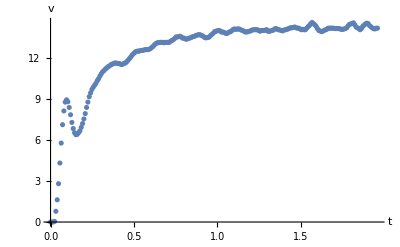

```mathematica
ListPlot[data2,AxesLabel->{t,v}]
```

```mathematica
Length[data2]
```

246

```mathematica
nlm2=NonlinearModelFit[data2,velSubExpr,{Bafter,Jafter,η},t]
```

General::munfl: -7880.72/(-6.21711062489832×10^463) is too small to represent as a normalized machine number; precision may be lost.

FittedModel[-0.413477 (-0.0935614 (-1.+2.71828^(-1717.91 t))+34.01 (-1.+2.71828^(-4.72596 t)))]

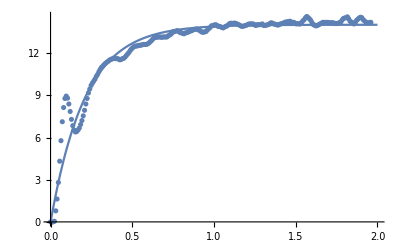

```mathematica
Show[Plot[nlm2[t],{t,0,2},PlotRange->All],ListPlot[data2], AxesOrigin->{0,0}]
```

```mathematica
nlm2["BestFitParameters"]
```

{Bafter→-6.6798,Jafter→4.46226,η→37.0173}

#### 3.3. Data Set 3

```mathematica
data3=Import["C:\RobotPhysics\3 Wheel Robot Encoder Rotational Velocity Test Data.xlsx",{"Data",3}]
```

{{0.,0.},{0.008,0.},{0.016,0.},{0.024,23.4375},{0.032,170.},{0.04,325.},{0.048,545.},{0.056,810.},{0.064,1060.},{0.072,1280.},{0.08,1450.},{0.088,1540.},{0.096,1540.},{0.104,1495.},{0.112,1415.},{0.12,1315.},{0.128,1230.},{0.136,1180.},{0.144,1155.},{0.152,1165.},{0.16,1200.},{0.168,1245.},{0.176,1290.},{0.184,1345.},{0.192,1395.},{0.2,1450.},{0.208,1505.},{0.216,1570.},{0.224,1625.},{0.232,1675.},{0.24,1715.},{0.248,1745.},{0.256,1770.},{0.264,1795.},{0.272,1825.},{0.28,1855.},{0.288,1895.},{0.296,1925.},{0.304,1955.},{0.312,1975.},{0.32,1995.},{0.328,2010.},{0.336,2020.},{0.344,2030.},{0.352,2045.},{0.36,2050.},{0.368,2050.},{0.376,2065.},{0.384,2065.},{0.392,2060.},{0.4,2065.},{0.408,2075.},{0.416,2070.},{0.424,2080.},{0.432,2095.},{0.44,2110.},{0.448,2120.},{0.456,2155.},{0.464,2195.},{0.472,2225.},{0.48,2250.},{0.488,2270.},{0.496,2260.},{0.504,2240.},{0.512,2225.},{0.52,2210.},{0.528,2205.},{0.536,2210.},{0.544,2215.},{0.552,2230.},{0.56,2245.},{0.568,2260.},{0.576,2280.},{0.584,2305.},{0.592,2315.},{0.6,2330.},{0.608,2340.},{0.616,2345.},{0.624,2345.},{0.632,2350.},{0.64,2355.},{0.648,2365.},{0.656,2370.},{0.664,2380.},{0.672,2395.},{0.68,2405.},{0.688,2405.},{0.696,2410.},{0.704,2405.},{0.712,2400.},{0.72,2385.},{0.728,2375.},{0.736,2380.},{0.744,2385.},{0.752,2380.},{0.76,2390.},{0.768,2405.},{0.776,2395.},{0.784,2395.},{0.792,2405.},{0.8,2410.},{0.808,2410.},{0.816,2420.},{0.824,2425.},{0.832,2425.},{0.84,2425.},{0.848,2425.},{0.856,2435.},{0.864,2435.},{0.872,2435.},{0.88,2435.},{0.888,2430.},{0.896,2410.},{0.904,2420.},{0.912,2420.},{0.92,2430.},{0.928,2450.},{0.936,2470.},{0.944,2460.},{0.952,2470.},{0.96,2470.},{0.968,2460.},{0.976,2485.},{0.984,2495.},{0.992,2495.},{1.,2490.},{1.008,2495.},{1.016,2450.},{1.024,2460.},{1.032,2470.},{1.04,2485.},{1.048,2495.},{1.056,2525.},{1.064,2525.},{1.072,2525.},{1.08,2520.},{1.088,2515.},{1.096,2510.},{1.104,2500.},{1.112,2490.},{1.12,2490.},{1.128,2485.},{1.136,2480.},{1.144,2485.},{1.152,2490.},{1.16,2490.},{1.168,2500.},{1.176,2505.},{1.184,2500.},{1.192,2495.},{1.2,2490.},{1.208,2480.},{1.216,2470.},{1.224,2470.},{1.232,2470.},{1.24,2470.},{1.248,2470.},{1.256,2480.},{1.264,2485.},{1.272,2495.},{1.28,2500.},{1.288,2505.},{1.296,2505.},{1.304,2505.},{1.312,2495.},{1.32,2500.},{1.328,2500.},{1.336,2505.},{1.344,2510.},{1.352,2520.},{1.36,2520.},{1.368,2530.},{1.376,2530.},{1.384,2530.},{1.392,2530.},{1.4,2530.},{1.408,2525.},{1.416,2525.},{1.424,2525.},{1.432,2525.},{1.44,2515.},{1.448,2505.},{1.456,2500.},{1.464,2495.},{1.472,2490.},{1.48,2495.},{1.488,2500.},{1.496,2490.},{1.504,2485.},{1.512,2480.},{1.52,2475.},{1.528,2470.},{1.536,2485.},{1.544,2495.},{1.552,2505.},{1.56,2520.},{1.568,2540.},{1.576,2550.},{1.584,2555.},{1.592,2565.},{1.6,2565.},{1.608,2555.},{1.616,2540.},{1.624,2535.},{1.632,2520.},{1.64,2515.},{1.648,2515.},{1.656,2525.},{1.664,2525.},{1.672,2530.},{1.68,2530.},{1.688,2530.},{1.696,2520.},{1.704,2520.},{1.712,2525.},{1.72,2525.},{1.728,2530.},{1.736,2535.},{1.744,2535.},{1.752,2520.},{1.76,2515.},{1.768,2500.},{1.776,2500.},{1.784,2490.},{1.792,2500.},{1.8,2510.},{1.808,2520.},{1.816,2520.},{1.824,2535.},{1.832,2540.},{1.84,2535.},{1.848,2540.},{1.856,2545.},{1.864,2545.},{1.872,2540.},{1.88,2540.},{1.888,2535.},{1.896,2520.},{1.904,2505.},{1.912,2500.},{1.92,2500.},{1.928,2500.},{1.936,2525.},{1.944,2555.},{1.952,2570.},{1.96,2585.}}

```mathematica
data3={#[[1]],2Pi/1120*#[[2]]}&/@data3
```

{{0.,0.},{0.008,0.},{0.016,0.},{0.024,0.131484},{0.032,0.953698},{0.04,1.82325},{0.048,3.05744},{0.056,4.54409},{0.064,5.94659},{0.072,7.18078},{0.08,8.13448},{0.088,8.63938},{0.096,8.63938},{0.104,8.38693},{0.112,7.93813},{0.12,7.37713},{0.128,6.90028},{0.136,6.61978},{0.144,6.47953},{0.152,6.53563},{0.16,6.73198},{0.168,6.98443},{0.176,7.23688},{0.184,7.54543},{0.192,7.82593},{0.2,8.13448},{0.208,8.44303},{0.216,8.80768},{0.224,9.11623},{0.232,9.39673},{0.24,9.62113},{0.248,9.78943},{0.256,9.92968},{0.264,10.0699},{0.272,10.2382},{0.28,10.4065},{0.288,10.6309},{0.296,10.7992},{0.304,10.9675},{0.312,11.0797},{0.32,11.1919},{0.328,11.2761},{0.336,11.3322},{0.344,11.3883},{0.352,11.4724},{0.36,11.5005},{0.368,11.5005},{0.376,11.5846},{0.384,11.5846},{0.392,11.5566},{0.4,11.5846},{0.408,11.6407},{0.416,11.6127},{0.424,11.6688},{0.432,11.7529},{0.44,11.8371},{0.448,11.8932},{0.456,12.0895},{0.464,12.3139},{0.472,12.4822},{0.48,12.6225},{0.488,12.7347},{0.496,12.6786},{0.504,12.5664},{0.512,12.4822},{0.52,12.3981},{0.528,12.37},{0.536,12.3981},{0.544,12.4261},{0.552,12.5103},{0.56,12.5944},{0.568,12.6786},{0.576,12.7908},{0.584,12.931},{0.592,12.9871},{0.6,13.0713},{0.608,13.1274},{0.616,13.1554},{0.624,13.1554},{0.632,13.1835},{0.64,13.2115},{0.648,13.2676},{0.656,13.2957},{0.664,13.3518},{0.672,13.4359},{0.68,13.492},{0.688,13.492},{0.696,13.5201},{0.704,13.492},{0.712,13.464},{0.72,13.3798},{0.728,13.3237},{0.736,13.3518},{0.744,13.3798},{0.752,13.3518},{0.76,13.4079},{0.768,13.492},{0.776,13.4359},{0.784,13.4359},{0.792,13.492},{0.8,13.5201},{0.808,13.5201},{0.816,13.5762},{0.824,13.6042},{0.832,13.6042},{0.84,13.6042},{0.848,13.6042},{0.856,13.6603},{0.864,13.6603},{0.872,13.6603},{0.88,13.6603},{0.888,13.6323},{0.896,13.5201},{0.904,13.5762},{0.912,13.5762},{0.92,13.6323},{0.928,13.7445},{0.936,13.8567},{0.944,13.8006},{0.952,13.8567},{0.96,13.8567},{0.968,13.8006},{0.976,13.9408},{0.984,13.9969},{0.992,13.9969},{1.,13.9689},{1.008,13.9969},{1.016,13.7445},{1.024,13.8006},{1.032,13.8567},{1.04,13.9408},{1.048,13.9969},{1.056,14.1652},{1.064,14.1652},{1.072,14.1652},{1.08,14.1372},{1.088,14.1091},{1.096,14.0811},{1.104,14.025},{1.112,13.9689},{1.12,13.9689},{1.128,13.9408},{1.136,13.9128},{1.144,13.9408},{1.152,13.9689},{1.16,13.9689},{1.168,14.025},{1.176,14.053},{1.184,14.025},{1.192,13.9969},{1.2,13.9689},{1.208,13.9128},{1.216,13.8567},{1.224,13.8567},{1.232,13.8567},{1.24,13.8567},{1.248,13.8567},{1.256,13.9128},{1.264,13.9408},{1.272,13.9969},{1.28,14.025},{1.288,14.053},{1.296,14.053},{1.304,14.053},{1.312,13.9969},{1.32,14.025},{1.328,14.025},{1.336,14.053},{1.344,14.0811},{1.352,14.1372},{1.36,14.1372},{1.368,14.1933},{1.376,14.1933},{1.384,14.1933},{1.392,14.1933},{1.4,14.1933},{1.408,14.1652},{1.416,14.1652},{1.424,14.1652},{1.432,14.1652},{1.44,14.1091},{1.448,14.053},{1.456,14.025},{1.464,13.9969},{1.472,13.9689},{1.48,13.9969},{1.488,14.025},{1.496,13.9689},{1.504,13.9408},{1.512,13.9128},{1.52,13.8847},{1.528,13.8567},{1.536,13.9408},{1.544,13.9969},{1.552,14.053},{1.56,14.1372},{1.568,14.2494},{1.576,14.3055},{1.584,14.3335},{1.592,14.3896},{1.6,14.3896},{1.608,14.3335},{1.616,14.2494},{1.624,14.2213},{1.632,14.1372},{1.64,14.1091},{1.648,14.1091},{1.656,14.1652},{1.664,14.1652},{1.672,14.1933},{1.68,14.1933},{1.688,14.1933},{1.696,14.1372},{1.704,14.1372},{1.712,14.1652},{1.72,14.1652},{1.728,14.1933},{1.736,14.2213},{1.744,14.2213},{1.752,14.1372},{1.76,14.1091},{1.768,14.025},{1.776,14.025},{1.784,13.9689},{1.792,14.025},{1.8,14.0811},{1.808,14.1372},{1.816,14.1372},{1.824,14.2213},{1.832,14.2494},{1.84,14.2213},{1.848,14.2494},{1.856,14.2774},{1.864,14.2774},{1.872,14.2494},{1.88,14.2494},{1.888,14.2213},{1.896,14.1372},{1.904,14.053},{1.912,14.025},{1.92,14.025},{1.928,14.025},{1.936,14.1652},{1.944,14.3335},{1.952,14.4177},{1.96,14.5018}}

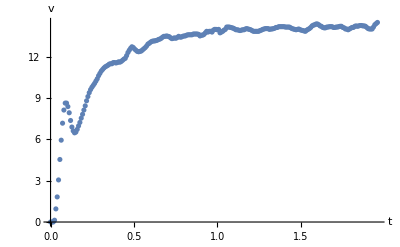

```mathematica
ListPlot[data3,AxesLabel->{t,v}]
```

```mathematica
Length[data3]
```

246

```mathematica
nlm3=NonlinearModelFit[data3,velSubExpr,{Bafter,Jafter,η},t]
```

FittedModel[-0.124753 (-0.323645 (-1.+2.71828^(-1717.75 t))+112.463 (-1.+2.71828^(-4.94331 t)))]

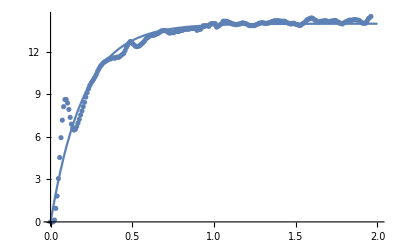

```mathematica
Show[Plot[nlm3[t],{t,0,2},PlotRange->All],ListPlot[data3], AxesOrigin->{0,0}]
```

```mathematica
nlm3["BestFitParameters"]
```

{Bafter→-1.99959,Jafter→1.29009,η→11.1663}

#### 3.4. Data Set 4

```mathematica
data4=Import["C:\RobotPhysics\3 Wheel Robot Encoder Rotational Velocity Test Data.xlsx",{"Data",4}]
```

{{0.,0.},{0.008,0.},{0.016,0.},{0.024,0.},{0.032,70.},{0.04,180.},{0.048,350.},{0.056,585.},{0.064,870.},{0.072,1120.},{0.08,1335.},{0.088,1490.},{0.096,1565.},{0.104,1555.},{0.112,1510.},{0.12,1430.},{0.128,1330.},{0.136,1240.},{0.144,1175.},{0.152,1135.},{0.16,1125.},{0.168,1140.},{0.176,1170.},{0.184,1215.},{0.192,1270.},{0.2,1325.},{0.208,1400.},{0.216,1485.},{0.224,1565.},{0.232,1640.},{0.24,1710.},{0.248,1760.},{0.256,1790.},{0.264,1810.},{0.272,1820.},{0.28,1835.},{0.288,1845.},{0.296,1855.},{0.304,1875.},{0.312,1905.},{0.32,1920.},{0.328,1945.},{0.336,1975.},{0.344,1995.},{0.352,2000.},{0.36,2020.},{0.368,2030.},{0.376,2035.},{0.384,2040.},{0.392,2060.},{0.4,2070.},{0.408,2080.},{0.416,2090.},{0.424,2110.},{0.432,2110.},{0.44,2115.},{0.448,2115.},{0.456,2125.},{0.464,2125.},{0.472,2140.},{0.48,2150.},{0.488,2170.},{0.496,2180.},{0.504,2190.},{0.512,2200.},{0.52,2210.},{0.528,2225.},{0.536,2245.},{0.544,2260.},{0.552,2270.},{0.56,2280.},{0.568,2275.},{0.576,2260.},{0.584,2255.},{0.592,2250.},{0.6,2255.},{0.608,2265.},{0.616,2280.},{0.624,2300.},{0.632,2320.},{0.64,2325.},{0.648,2335.},{0.656,2350.},{0.664,2345.},{0.672,2345.},{0.68,2345.},{0.688,2340.},{0.696,2335.},{0.704,2345.},{0.712,2350.},{0.72,2365.},{0.728,2380.},{0.736,2385.},{0.744,2390.},{0.752,2395.},{0.76,2400.},{0.768,2405.},{0.776,2415.},{0.784,2410.},{0.792,2405.},{0.8,2390.},{0.808,2375.},{0.816,2360.},{0.824,2365.},{0.832,2370.},{0.84,2380.},{0.848,2395.},{0.856,2410.},{0.864,2415.},{0.872,2425.},{0.88,2435.},{0.888,2435.},{0.896,2435.},{0.904,2430.},{0.912,2420.},{0.92,2415.},{0.928,2415.},{0.936,2420.},{0.944,2430.},{0.952,2440.},{0.96,2445.},{0.968,2455.},{0.976,2465.},{0.984,2480.},{0.992,2495.},{1.,2510.},{1.008,2520.},{1.016,2520.},{1.024,2515.},{1.032,2505.},{1.04,2495.},{1.048,2485.},{1.056,2485.},{1.064,2485.},{1.072,2495.},{1.08,2505.},{1.088,2515.},{1.096,2515.},{1.104,2515.},{1.112,2510.},{1.12,2510.},{1.128,2515.},{1.136,2520.},{1.144,2525.},{1.152,2530.},{1.16,2520.},{1.168,2505.},{1.176,2500.},{1.184,2490.},{1.192,2480.},{1.2,2485.},{1.208,2490.},{1.216,2485.},{1.224,2490.},{1.232,2500.},{1.24,2505.},{1.248,2500.},{1.256,2505.},{1.264,2500.},{1.272,2485.},{1.28,2470.},{1.288,2475.},{1.296,2470.},{1.304,2475.},{1.312,2490.},{1.32,2505.},{1.328,2505.},{1.336,2515.},{1.344,2520.},{1.352,2515.},{1.36,2510.},{1.368,2515.},{1.376,2515.},{1.384,2515.},{1.392,2520.},{1.4,2525.},{1.408,2525.},{1.416,2520.},{1.424,2520.},{1.432,2520.},{1.44,2520.},{1.448,2520.},{1.456,2530.},{1.464,2530.},{1.472,2525.},{1.48,2525.},{1.488,2515.},{1.496,2500.},{1.504,2490.},{1.512,2490.},{1.52,2480.},{1.528,2505.},{1.536,2520.},{1.544,2540.},{1.552,2560.},{1.56,2580.},{1.568,2555.},{1.576,2550.},{1.584,2535.},{1.592,2510.},{1.6,2495.},{1.608,2505.},{1.616,2500.},{1.624,2505.},{1.632,2515.},{1.64,2520.},{1.648,2515.},{1.656,2530.},{1.664,2530.},{1.672,2535.},{1.68,2535.},{1.688,2550.},{1.696,2535.},{1.704,2535.},{1.712,2530.},{1.72,2535.},{1.728,2520.},{1.736,2525.},{1.744,2525.},{1.752,2530.},{1.76,2530.},{1.768,2545.},{1.776,2555.},{1.784,2570.},{1.792,2570.},{1.8,2570.},{1.808,2560.},{1.816,2555.},{1.824,2535.},{1.832,2530.},{1.84,2525.},{1.848,2525.},{1.856,2520.},{1.864,2530.},{1.872,2535.},{1.88,2540.},{1.888,2550.},{1.896,2555.},{1.904,2555.},{1.912,2550.},{1.92,2545.},{1.928,2530.},{1.936,2520.},{1.944,2510.},{1.952,2515.},{1.96,2515.}}

```mathematica
data4={#[[1]],2Pi/1120*#[[2]]}&/@data4
```

{{0.,0.},{0.008,0.},{0.016,0.},{0.024,0.},{0.032,0.392699},{0.04,1.0098},{0.048,1.9635},{0.056,3.28184},{0.064,4.88069},{0.072,6.28319},{0.08,7.48933},{0.088,8.35888},{0.096,8.77963},{0.104,8.72353},{0.112,8.47108},{0.12,8.02228},{0.128,7.46128},{0.136,6.95638},{0.144,6.59173},{0.152,6.36734},{0.16,6.31124},{0.168,6.39539},{0.176,6.56368},{0.184,6.81613},{0.192,7.12468},{0.2,7.43323},{0.208,7.85398},{0.216,8.33083},{0.224,8.77963},{0.232,9.20038},{0.24,9.59308},{0.248,9.87358},{0.256,10.0419},{0.264,10.1541},{0.272,10.2102},{0.28,10.2943},{0.288,10.3504},{0.296,10.4065},{0.304,10.5187},{0.312,10.687},{0.32,10.7712},{0.328,10.9114},{0.336,11.0797},{0.344,11.1919},{0.352,11.22},{0.36,11.3322},{0.368,11.3883},{0.376,11.4163},{0.384,11.4444},{0.392,11.5566},{0.4,11.6127},{0.408,11.6688},{0.416,11.7249},{0.424,11.8371},{0.432,11.8371},{0.44,11.8651},{0.448,11.8651},{0.456,11.9212},{0.464,11.9212},{0.472,12.0054},{0.48,12.0615},{0.488,12.1737},{0.496,12.2298},{0.504,12.2859},{0.512,12.342},{0.52,12.3981},{0.528,12.4822},{0.536,12.5944},{0.544,12.6786},{0.552,12.7347},{0.56,12.7908},{0.568,12.7627},{0.576,12.6786},{0.584,12.6505},{0.592,12.6225},{0.6,12.6505},{0.608,12.7066},{0.616,12.7908},{0.624,12.903},{0.632,13.0152},{0.64,13.0432},{0.648,13.0993},{0.656,13.1835},{0.664,13.1554},{0.672,13.1554},{0.68,13.1554},{0.688,13.1274},{0.696,13.0993},{0.704,13.1554},{0.712,13.1835},{0.72,13.2676},{0.728,13.3518},{0.736,13.3798},{0.744,13.4079},{0.752,13.4359},{0.76,13.464},{0.768,13.492},{0.776,13.5481},{0.784,13.5201},{0.792,13.492},{0.8,13.4079},{0.808,13.3237},{0.816,13.2396},{0.824,13.2676},{0.832,13.2957},{0.84,13.3518},{0.848,13.4359},{0.856,13.5201},{0.864,13.5481},{0.872,13.6042},{0.88,13.6603},{0.888,13.6603},{0.896,13.6603},{0.904,13.6323},{0.912,13.5762},{0.92,13.5481},{0.928,13.5481},{0.936,13.5762},{0.944,13.6323},{0.952,13.6884},{0.96,13.7164},{0.968,13.7725},{0.976,13.8286},{0.984,13.9128},{0.992,13.9969},{1.,14.0811},{1.008,14.1372},{1.016,14.1372},{1.024,14.1091},{1.032,14.053},{1.04,13.9969},{1.048,13.9408},{1.056,13.9408},{1.064,13.9408},{1.072,13.9969},{1.08,14.053},{1.088,14.1091},{1.096,14.1091},{1.104,14.1091},{1.112,14.0811},{1.12,14.0811},{1.128,14.1091},{1.136,14.1372},{1.144,14.1652},{1.152,14.1933},{1.16,14.1372},{1.168,14.053},{1.176,14.025},{1.184,13.9689},{1.192,13.9128},{1.2,13.9408},{1.208,13.9689},{1.216,13.9408},{1.224,13.9689},{1.232,14.025},{1.24,14.053},{1.248,14.025},{1.256,14.053},{1.264,14.025},{1.272,13.9408},{1.28,13.8567},{1.288,13.8847},{1.296,13.8567},{1.304,13.8847},{1.312,13.9689},{1.32,14.053},{1.328,14.053},{1.336,14.1091},{1.344,14.1372},{1.352,14.1091},{1.36,14.0811},{1.368,14.1091},{1.376,14.1091},{1.384,14.1091},{1.392,14.1372},{1.4,14.1652},{1.408,14.1652},{1.416,14.1372},{1.424,14.1372},{1.432,14.1372},{1.44,14.1372},{1.448,14.1372},{1.456,14.1933},{1.464,14.1933},{1.472,14.1652},{1.48,14.1652},{1.488,14.1091},{1.496,14.025},{1.504,13.9689},{1.512,13.9689},{1.52,13.9128},{1.528,14.053},{1.536,14.1372},{1.544,14.2494},{1.552,14.3616},{1.56,14.4738},{1.568,14.3335},{1.576,14.3055},{1.584,14.2213},{1.592,14.0811},{1.6,13.9969},{1.608,14.053},{1.616,14.025},{1.624,14.053},{1.632,14.1091},{1.64,14.1372},{1.648,14.1091},{1.656,14.1933},{1.664,14.1933},{1.672,14.2213},{1.68,14.2213},{1.688,14.3055},{1.696,14.2213},{1.704,14.2213},{1.712,14.1933},{1.72,14.2213},{1.728,14.1372},{1.736,14.1652},{1.744,14.1652},{1.752,14.1933},{1.76,14.1933},{1.768,14.2774},{1.776,14.3335},{1.784,14.4177},{1.792,14.4177},{1.8,14.4177},{1.808,14.3616},{1.816,14.3335},{1.824,14.2213},{1.832,14.1933},{1.84,14.1652},{1.848,14.1652},{1.856,14.1372},{1.864,14.1933},{1.872,14.2213},{1.88,14.2494},{1.888,14.3055},{1.896,14.3335},{1.904,14.3335},{1.912,14.3055},{1.92,14.2774},{1.928,14.1933},{1.936,14.1372},{1.944,14.0811},{1.952,14.1091},{1.96,14.1091}}

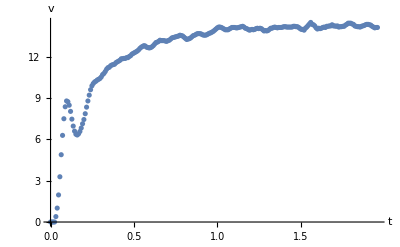

```mathematica
ListPlot[data4,AxesLabel->{t,v}]
```

```mathematica
Length[data4]
```

246

```mathematica
nlm4=NonlinearModelFit[data4,velSubExpr,{Bafter,Jafter,η},t]
```

General::munfl: -7860.04/(-1.31548073128744×10^535) is too small to represent as a normalized machine number; precision may be lost.

FittedModel[-0.00189494 (-19.9747 (-1.+2.71828^(-1717.99 t))+7422.95 (-1.+2.71828^(-4.623 t)))]

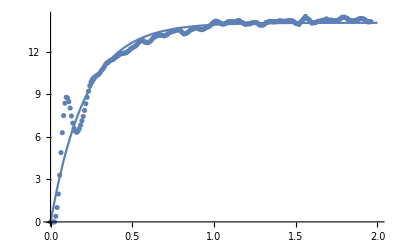

```mathematica
Show[Plot[nlm4[t],{t,0,2},PlotRange->All],ListPlot[data4], AxesOrigin->{0,0}]
```

```mathematica
nlm4["BestFitParameters"]
```

{Bafter→-0.0306472,Jafter→0.0209003,η→0.169666}

#### 3.5. Data Set 5

```mathematica
data5=Import["C:\RobotPhysics\3 Wheel Robot Encoder Rotational Velocity Test Data.xlsx",{"Data",5}]
```

{{0.,0.},{0.008,0.},{0.016,180.556},{0.024,500.},{0.032,800.},{0.04,1065.},{0.048,1300.},{0.056,1485.},{0.064,1600.},{0.072,1640.},{0.08,1620.},{0.088,1560.},{0.096,1480.},{0.104,1400.},{0.112,1335.},{0.12,1280.},{0.128,1250.},{0.136,1240.},{0.144,1225.},{0.152,1230.},{0.16,1260.},{0.168,1300.},{0.176,1350.},{0.184,1435.},{0.192,1515.},{0.2,1585.},{0.208,1645.},{0.216,1700.},{0.224,1730.},{0.232,1760.},{0.24,1795.},{0.248,1830.},{0.256,1855.},{0.264,1890.},{0.272,1915.},{0.28,1935.},{0.288,1950.},{0.296,1970.},{0.304,1985.},{0.312,2005.},{0.32,2025.},{0.328,2050.},{0.336,2070.},{0.344,2085.},{0.352,2095.},{0.36,2100.},{0.368,2100.},{0.376,2100.},{0.384,2110.},{0.392,2110.},{0.4,2120.},{0.408,2130.},{0.416,2145.},{0.424,2140.},{0.432,2160.},{0.44,2160.},{0.448,2160.},{0.456,2165.},{0.464,2180.},{0.472,2180.},{0.48,2190.},{0.488,2205.},{0.496,2205.},{0.504,2210.},{0.512,2215.},{0.52,2230.},{0.528,2240.},{0.536,2260.},{0.544,2270.},{0.552,2290.},{0.56,2295.},{0.568,2300.},{0.576,2300.},{0.584,2310.},{0.592,2300.},{0.6,2295.},{0.608,2300.},{0.616,2305.},{0.624,2305.},{0.632,2320.},{0.64,2345.},{0.648,2350.},{0.656,2355.},{0.664,2360.},{0.672,2360.},{0.68,2345.},{0.688,2345.},{0.696,2345.},{0.704,2350.},{0.712,2360.},{0.72,2375.},{0.728,2385.},{0.736,2395.},{0.744,2405.},{0.752,2405.},{0.76,2410.},{0.768,2415.},{0.776,2420.},{0.784,2415.},{0.792,2420.},{0.8,2420.},{0.808,2430.},{0.816,2440.},{0.824,2460.},{0.832,2470.},{0.84,2480.},{0.848,2475.},{0.856,2475.},{0.864,2470.},{0.872,2475.},{0.88,2475.},{0.888,2480.},{0.896,2485.},{0.904,2480.},{0.912,2470.},{0.92,2470.},{0.928,2470.},{0.936,2450.},{0.944,2450.},{0.952,2450.},{0.96,2445.},{0.968,2440.},{0.976,2460.},{0.984,2475.},{0.992,2480.},{1.,2490.},{1.008,2495.},{1.016,2490.},{1.024,2470.},{1.032,2470.},{1.04,2460.},{1.048,2460.},{1.056,2460.},{1.064,2480.},{1.072,2490.},{1.08,2505.},{1.088,2520.},{1.096,2530.},{1.104,2520.},{1.112,2510.},{1.12,2515.},{1.128,2495.},{1.136,2485.},{1.144,2495.},{1.152,2500.},{1.16,2475.},{1.168,2490.},{1.176,2500.},{1.184,2495.},{1.192,2505.},{1.2,2535.},{1.208,2540.},{1.216,2550.},{1.224,2560.},{1.232,2560.},{1.24,2545.},{1.248,2535.},{1.256,2515.},{1.264,2505.},{1.272,2495.},{1.28,2500.},{1.288,2510.},{1.296,2525.},{1.304,2540.},{1.312,2550.},{1.32,2550.},{1.328,2545.},{1.336,2540.},{1.344,2525.},{1.352,2515.},{1.36,2515.},{1.368,2510.},{1.376,2505.},{1.384,2505.},{1.392,2505.},{1.4,2505.},{1.408,2510.},{1.416,2520.},{1.424,2525.},{1.432,2530.},{1.44,2525.},{1.448,2515.},{1.456,2500.},{1.464,2495.},{1.472,2485.},{1.48,2485.},{1.488,2495.},{1.496,2510.},{1.504,2525.},{1.512,2550.},{1.52,2565.},{1.528,2575.},{1.536,2575.},{1.544,2565.},{1.552,2550.},{1.56,2535.},{1.568,2520.},{1.576,2505.},{1.584,2495.},{1.592,2485.},{1.6,2485.},{1.608,2485.},{1.616,2495.},{1.624,2500.},{1.632,2515.},{1.64,2520.},{1.648,2535.},{1.656,2540.},{1.664,2555.},{1.672,2560.},{1.68,2570.},{1.688,2560.},{1.696,2555.},{1.704,2545.},{1.712,2530.},{1.72,2525.},{1.728,2525.},{1.736,2530.},{1.744,2540.},{1.752,2550.},{1.76,2550.},{1.768,2560.},{1.776,2560.},{1.784,2555.},{1.792,2550.},{1.8,2545.},{1.808,2535.},{1.816,2530.},{1.824,2525.},{1.832,2535.},{1.84,2540.},{1.848,2550.},{1.856,2560.},{1.864,2570.},{1.872,2565.},{1.88,2560.},{1.888,2545.},{1.896,2530.},{1.904,2510.},{1.912,2495.},{1.92,2495.},{1.928,2500.},{1.936,2505.},{1.944,2515.},{1.952,2530.},{1.96,2530.}}

```mathematica
data5={#[[1]],2Pi/1120*#[[2]]}&/@data5
```

{{0.,0.},{0.008,0.},{0.016,1.01291},{0.024,2.80499},{0.032,4.48799},{0.04,5.97464},{0.048,7.29298},{0.056,8.33083},{0.064,8.97598},{0.072,9.20038},{0.08,9.08818},{0.088,8.75158},{0.096,8.30278},{0.104,7.85398},{0.112,7.48933},{0.12,7.18078},{0.128,7.01248},{0.136,6.95638},{0.144,6.87223},{0.152,6.90028},{0.16,7.06858},{0.168,7.29298},{0.176,7.57348},{0.184,8.05033},{0.192,8.49913},{0.2,8.89183},{0.208,9.22843},{0.216,9.53698},{0.224,9.70528},{0.232,9.87358},{0.24,10.0699},{0.248,10.2663},{0.256,10.4065},{0.264,10.6029},{0.272,10.7431},{0.28,10.8553},{0.288,10.9395},{0.296,11.0517},{0.304,11.1358},{0.312,11.248},{0.32,11.3602},{0.328,11.5005},{0.336,11.6127},{0.344,11.6968},{0.352,11.7529},{0.36,11.781},{0.368,11.781},{0.376,11.781},{0.384,11.8371},{0.392,11.8371},{0.4,11.8932},{0.408,11.9493},{0.416,12.0334},{0.424,12.0054},{0.432,12.1176},{0.44,12.1176},{0.448,12.1176},{0.456,12.1456},{0.464,12.2298},{0.472,12.2298},{0.48,12.2859},{0.488,12.37},{0.496,12.37},{0.504,12.3981},{0.512,12.4261},{0.52,12.5103},{0.528,12.5664},{0.536,12.6786},{0.544,12.7347},{0.552,12.8469},{0.56,12.8749},{0.568,12.903},{0.576,12.903},{0.584,12.9591},{0.592,12.903},{0.6,12.8749},{0.608,12.903},{0.616,12.931},{0.624,12.931},{0.632,13.0152},{0.64,13.1554},{0.648,13.1835},{0.656,13.2115},{0.664,13.2396},{0.672,13.2396},{0.68,13.1554},{0.688,13.1554},{0.696,13.1554},{0.704,13.1835},{0.712,13.2396},{0.72,13.3237},{0.728,13.3798},{0.736,13.4359},{0.744,13.492},{0.752,13.492},{0.76,13.5201},{0.768,13.5481},{0.776,13.5762},{0.784,13.5481},{0.792,13.5762},{0.8,13.5762},{0.808,13.6323},{0.816,13.6884},{0.824,13.8006},{0.832,13.8567},{0.84,13.9128},{0.848,13.8847},{0.856,13.8847},{0.864,13.8567},{0.872,13.8847},{0.88,13.8847},{0.888,13.9128},{0.896,13.9408},{0.904,13.9128},{0.912,13.8567},{0.92,13.8567},{0.928,13.8567},{0.936,13.7445},{0.944,13.7445},{0.952,13.7445},{0.96,13.7164},{0.968,13.6884},{0.976,13.8006},{0.984,13.8847},{0.992,13.9128},{1.,13.9689},{1.008,13.9969},{1.016,13.9689},{1.024,13.8567},{1.032,13.8567},{1.04,13.8006},{1.048,13.8006},{1.056,13.8006},{1.064,13.9128},{1.072,13.9689},{1.08,14.053},{1.088,14.1372},{1.096,14.1933},{1.104,14.1372},{1.112,14.0811},{1.12,14.1091},{1.128,13.9969},{1.136,13.9408},{1.144,13.9969},{1.152,14.025},{1.16,13.8847},{1.168,13.9689},{1.176,14.025},{1.184,13.9969},{1.192,14.053},{1.2,14.2213},{1.208,14.2494},{1.216,14.3055},{1.224,14.3616},{1.232,14.3616},{1.24,14.2774},{1.248,14.2213},{1.256,14.1091},{1.264,14.053},{1.272,13.9969},{1.28,14.025},{1.288,14.0811},{1.296,14.1652},{1.304,14.2494},{1.312,14.3055},{1.32,14.3055},{1.328,14.2774},{1.336,14.2494},{1.344,14.1652},{1.352,14.1091},{1.36,14.1091},{1.368,14.0811},{1.376,14.053},{1.384,14.053},{1.392,14.053},{1.4,14.053},{1.408,14.0811},{1.416,14.1372},{1.424,14.1652},{1.432,14.1933},{1.44,14.1652},{1.448,14.1091},{1.456,14.025},{1.464,13.9969},{1.472,13.9408},{1.48,13.9408},{1.488,13.9969},{1.496,14.0811},{1.504,14.1652},{1.512,14.3055},{1.52,14.3896},{1.528,14.4457},{1.536,14.4457},{1.544,14.3896},{1.552,14.3055},{1.56,14.2213},{1.568,14.1372},{1.576,14.053},{1.584,13.9969},{1.592,13.9408},{1.6,13.9408},{1.608,13.9408},{1.616,13.9969},{1.624,14.025},{1.632,14.1091},{1.64,14.1372},{1.648,14.2213},{1.656,14.2494},{1.664,14.3335},{1.672,14.3616},{1.68,14.4177},{1.688,14.3616},{1.696,14.3335},{1.704,14.2774},{1.712,14.1933},{1.72,14.1652},{1.728,14.1652},{1.736,14.1933},{1.744,14.2494},{1.752,14.3055},{1.76,14.3055},{1.768,14.3616},{1.776,14.3616},{1.784,14.3335},{1.792,14.3055},{1.8,14.2774},{1.808,14.2213},{1.816,14.1933},{1.824,14.1652},{1.832,14.2213},{1.84,14.2494},{1.848,14.3055},{1.856,14.3616},{1.864,14.4177},{1.872,14.3896},{1.88,14.3616},{1.888,14.2774},{1.896,14.1933},{1.904,14.0811},{1.912,13.9969},{1.92,13.9969},{1.928,14.025},{1.936,14.053},{1.944,14.1091},{1.952,14.1933},{1.96,14.1933}}

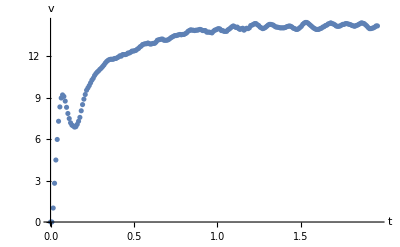

```mathematica
ListPlot[data5,AxesLabel->{t,v}]
```

```mathematica
Length[data5]
```

246

```mathematica
nlm5=NonlinearModelFit[data5,velSubExpr,{Bafter,Jafter,η},t]
```

FittedModel[-3.23428 (-0.014331 (-1.+2.71828^(-1717.17 t))+4.32403 (-1.+2.71828^(-5.69117 t)))]

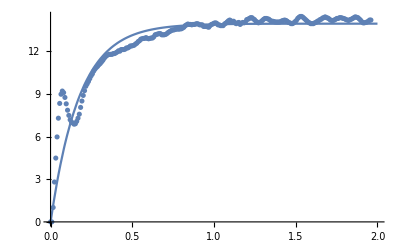

```mathematica
Show[Plot[nlm5[t],{t,0,2},PlotRange->All],ListPlot[data5], AxesOrigin->{0,0}]
```

```mathematica
nlm5["BestFitParameters"]
```

{Bafter→-51.1967,Jafter→29.1437,η→289.266}

## Section. Revision History

2018.08.26. Initial version.

2018.08.28. Added velocity expression.  Added motor data.  Created NonlinearModelFit for the data.

2018.08.29. Fixed issue with some variables not being plugged in to velAfterStepGeneric. Changed units on data from ticks / sec to rad / sec.

2018.08.30. Fixed drastically incorrect scale on fit (issue was due to some constants being specified with incorrect units or after the gearbox instead of before).

2018.09.12. Added 4 more encoder velocity data sets from 3 wheel test robot and analyzed them.